```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
```

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
M=.;a=.;
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}];
TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}];
christoffel[[2,1,1]]
christoffel[[2,1,1]] /. r-> 4 /. θ -> π/4
christoffel[[2,2,2]]  /. r-> 4 /. θ -> π/4
```

-(M (a^2+r (-2 M+r)) (-r^2+a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)

-((-16+a^2/2) (a^2+4 (4-2 M)) M)/((16+a^2/2)^3)

(4 (a^2-4 M)+1/2 a^2 (-4+M))/((16+a^2/2) (a^2+4 (4-2 M)))

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(r[τ]≤1.01*rplus),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
(* This one calculates u dot u *)
udotu[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];
xα=xα/.τ->τval;uα=uα/.τ->τval;uα.((metric/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
(* And this one prints out the coordinates *)
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

4000000

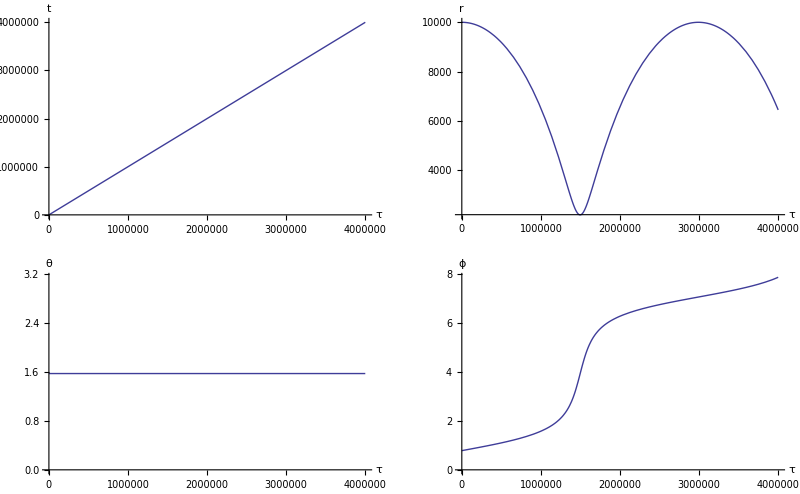

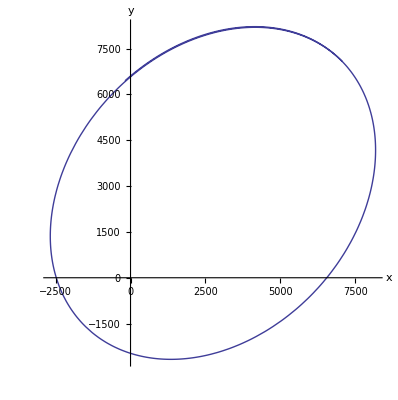

```mathematica
uinvar=-1; (* define u dot u to be -1 for massive particles *)
M=1;a=0.99 M;
maxτ=4000000;
(* check orbits very far away from the black hole *)
soln=computeSoln[maxτ,{0,0,0.0000006},{0,10000,π/2,Pi/4}];
τend
xyzsoln=sphslnToCartsln[soln];
GraphicsGrid[{{Plot[Evaluate[coords[[1]][τ]/.soln],{τ,0,τend},AxesLabel->{"τ","t"}],Plot[Evaluate[coords[[2]][τ]/.soln],{τ,0,τend},AxesLabel->{"τ","r"}]},{Plot[Evaluate[coords[[3]][τ]/.soln],{τ,0,τend},AxesLabel->{"τ","θ"}],Plot[Evaluate[coords[[4]][τ]/.soln],{τ,0,τend},AxesLabel->{"τ","ϕ"}]}}]
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},AxesLabel->{x,y}]
```

```mathematica
(* Define various plotting functions *)
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

For initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,-0.02} the particle crosses the horizon at τend=60.6235

For initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,-0.015} the particle crosses the horizon at τend=51.3499

For initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,-0.01} the particle crosses the horizon at τend=47.147

For initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,-0.005} the particle crosses the horizon at τend=45.4137

For initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,0.} the particle crosses the horizon at τend=45.4372

For initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,0.005} the particle crosses the horizon at τend=47.2766

For initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,0.01} the particle crosses the horizon at τend=52.3353

The particle did not cross the horizon for initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,0.015}

The particle did not cross the horizon for initial coordinates={0,12,π/2,π/4} and initial velocities={0,0,0.02}

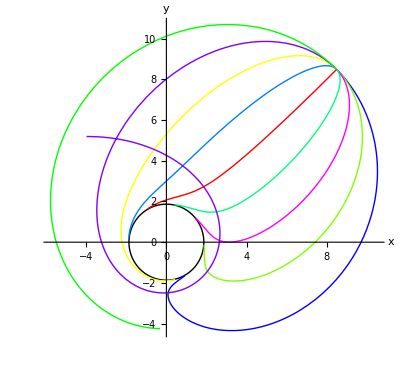

```mathematica
(* Check trajectories of massive particles for slightly different initial velocities *)
τend=.;uinvar = -1;
M=1;a=0.5;rplus=M+Sqrt[M^2-a^2];
ivs={0,0,0};ics={0,12,π/2,Pi/4};
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot = 75;
Table[genXYPlot[τPlot,{0,12,π/2,π/4},{0,0,0+i*0.01},1-i*(5/6)],{i,-2,2,0.5}];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y}]
```

The particle did not cross the horizon for initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.01}

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.009} the particle crosses the horizon at τend=104.453

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.008} the particle crosses the horizon at τend=84.6136

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.007} the particle crosses the horizon at τend=77.7713

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.006} the particle crosses the horizon at τend=74.1494

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.005} the particle crosses the horizon at τend=72.1333

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.004} the particle crosses the horizon at τend=71.1867

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.003} the particle crosses the horizon at τend=71.1245

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.002} the particle crosses the horizon at τend=71.9655

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,-0.001} the particle crosses the horizon at τend=73.9737

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.} the particle crosses the horizon at τend=78.0594

For initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.001} the particle crosses the horizon at τend=89.962

The particle did not cross the horizon for initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.002}

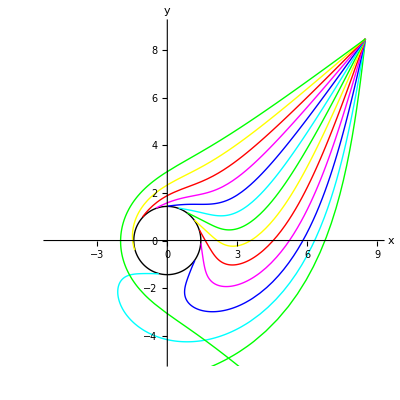

```mathematica
(* Do the same but for photons *)
τend=.;uinvar = 0;
M=1;a=0.9;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=150;
Table[genXYPlot[τPlot,{0,12,π/2,π/4},{-0.15,0,0+i*0.001},1-i*(5/6)],{i,-10,2,1}];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-5,9},{-5,9}}]
```

```mathematica
τend=.;uinvar = -1;
M=1;a=0.99;rplus=M+Sqrt[M^2-a^2];
ivs={-0.01,0.01,0.017};ics={0,10,π/3,Pi/4};
horizpl=SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity,PlotPoints->50];
τPlot = 100;
Table[genXYZPlot[τPlot,{0,10,π/3,π/4},{-0.01,0.01,0+i*0.017},1-i*(5/6)],{i,-2,2,1}];
Show[%,horizpl]
```

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.01,0.01,-0.034} the particle crosses the horizon at τend=46.1444

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.01,0.01,-0.017} the particle crosses the horizon at τend=36.2129

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.01,0.01,0.} the particle crosses the horizon at τend=37.9748

The particle did not cross the horizon for initial coordinates={0,10,π/3,π/4} and initial velocities={-0.01,0.01,0.017}

The particle did not cross the horizon for initial coordinates={0,10,π/3,π/4} and initial velocities={-0.01,0.01,0.034}

-Graphics3D-

```mathematica
τend=.;uinvar = 0;
M=1;a=0.99;rplus=M+Sqrt[M^2-a^2];
ivs={-0.15,0.01,0.017};ics={0,10,π/3,Pi/4};
horizpl=SphericalPlot3D[{rplus,EdgeForm[]},{θ,0,Pi},{ϕ,0, 2Pi},DisplayFunction->Identity,PlotPoints->50];
τPlot = 300;
Table[genXYZPlot[τPlot,{0,10,π/3,π/4},{-0.05,0.001,0+i*0.001},1-i*(5/6)],{i,-2,2,1}];
Show[%,horizpl]
```

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,-0.002} the particle crosses the horizon at τend=180.943

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,-0.001} the particle crosses the horizon at τend=190.31

For initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.} the particle crosses the horizon at τend=239.611

The particle did not cross the horizon for initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.001}

The particle did not cross the horizon for initial coordinates={0,10,π/3,π/4} and initial velocities={-0.05,0.001,0.002}

-Graphics3D-

The particle did not cross the horizon for initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.00146}

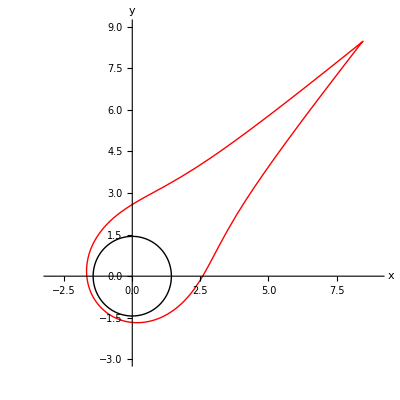

```mathematica
τend=.;uinvar = 0;
M=1;a=0.9;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=190;
genXYPlot[τPlot,{0,12,π/2,π/4},{-0.15,0,0.00146},1];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-3,9},{-3,9}}]
```

The particle did not cross the horizon for initial coordinates={0,12,π/2,π/4} and initial velocities={-0.15,0,0.0012728}

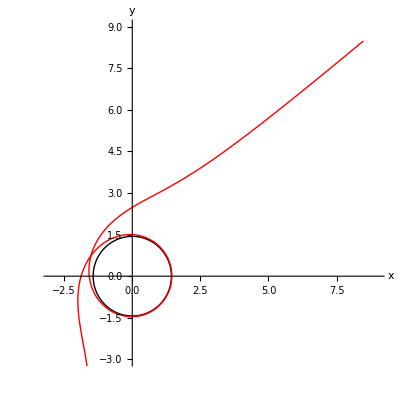

```mathematica
τend=.;uinvar = 0;
M=1;a=0.9;rplus=M+Sqrt[M^2-a^2];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=190;
genXYPlot[τPlot,{0,12,π/2,π/4},{-0.15,0,0.0012728},1];
(*Manipulate[Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-coordMax,coordMax},{-coordMax,coordMax}}],{coordMax,2,10}]*)
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-3,9},{-3,9}}]
```